## The Composability of Universal Logic Gates: and their connections to Universal Properties

## Abstract

It is well-known that simple logic gates, such as NAND, can be composed into arbitrary logical functions, even construct the full range of computable functions, including the so-called Turing Complete Machine. The range of computable functions, in practice, includes all functions that an Arithmetic Logic Unit (ALU) of a general purpose Computers can compute. For example, adding, subtraction, communication circuit switching, and keeping information content in memory. All these computational functionalities can be composed of one kind of simple logic gate, NAND. It is known NAND, NOR, and others, a total of 6 out of 16 possible 2-input, 1-output Logic Gates (basic gates), are Universal Logic Gates. By performing literature research in the area of Category Theory, Universal Algebra, and more specifically, Wiring Diagram (WD)Operad. In other words, using WD Operad, one may leverage the universal compositional properties of 2-input, 1-output Logic Gates can be extended to represent arbitrary m-input, n-output discrete-valued systems or equivalently, software defined computable functions. However, the composition and verification of computable functions are usually considered to be done through extensive human reasoning, and over time, engineered into a collection of solution database to be used for further solutions. This article shows that WD Operad can be used as a unifying compositional framework to automate the efforts of wiring diagram composition. It allows various computable functions to be discovered by an mechanical (Operadic) search strategy. Therefore, the compositional efforts can also be universally applied to create arbitrarily defined computable functions. The systematic process of extending 2-input,1-output to m-input,n-output system based on Category Theory also provides a generic method to analyze and synthesize other complex functions, therefore offers a universal reasoning framework to solve many problems in mathematics, database management, knowledge engineering, quantum information theory, that used to require a lot more human mental efforts without adopting this enumeration-based computational approach.

## Introduction

In the world of 2-input, 1-output binary-valued logic gates, there are total of 16 possible gates, or boolean functions.  Based on the principle of universal computability, these 16 possible two-input binary-value compositional functions, provides the symbolic basis for executing all computable functions in the digital space. Out of these 16 possible different functions, 6 of them, such as NAND, NOR, Not(A) or B, ..., are considered to be “universal”. In other words, any other logical functions can be composed of one of these six basic logical building blocks. Therefore, this class of logical functions are considered to be “universal”. In practice, most industrial experts chooses NAND gate to represent this group of six universal gates. This paper explains why these gates are univerasl, and where the universality comes from.

This paper will present the information in the following three steps.
0. A brief literature review, setting the context and intellectual framing of why compositionality is the core of science of complexity.
1. Present the full set of 2-input, 1-output Logic Functions, and classify them into Universal and Non-Univeresal Gates. 
2. Introduce the rule of composition, demonstrate how one type of logic gate can be composed into other equivalent gate using a set of composition operators, in category theoretical terms, following Spivak’s Operad calculus.
3. Demonstrate the Universal properties of the 6 logic gates out of the total collection of 16 possible gates.
4. Present other “Universal Properties” in other branches of Maths, and demonstrate their relationship in terms of Compositionality of Universal Logic Gates.
5. Identify applications of Universal Properties and Composability, in the areas of Maths, Physics, Engineering, and Humanity in terms of universal properties.

## Literature Review

In Shannon’s 1937 Master Thesis, “A Symbolic Analysis of Relay and Switching Circuits”, he demonstrated a connection between Boolean Algebra and Digital Circuit Design. Formulaic boolean computation can be mapped onto the behavior of Binary Valued Logic Gates. This observation was ground breaking from both theoretical and application viewpoints. Shannon’s formulation provides a bridge for mathematicians and engineers, to explore computation from two structurally equivalent, but implementation wise totally different angles. The contributions of establishing a class of isomorphisms between the behavior of digital logic circuits, and boolean algebraic equations, can be understood on two levels. First,  when engineers compose simple logic gates together to form another logical function unit, they could just as well write down mathematical formulas, and perform analysis and synthesis of possible values in writing. Therefore, computation can be “conceptually elevated” into algebraic operations, the results would be identical, but the computation happens not on the boolean values, but on the structure of the formula. Second, once the boolean algebraic formula has been simplified or “solved”, the actual boolean value assessment of the formulaic function, can be “physically grounded” to the logical devices, value assessment would be “automatically” computed using the equivalent circuitry, without having to be mindfully computed using human heads. 

This bi-directional isomorphism between Boolean Algebra and Digital Logic, is a special case for the Adjoint mechanism between mathematical and physical systems. It is this adjoint relationship, that enables simulation and evaluation of complex mathematical ideas, onto devices that can perform large scale computation tirelessly. The expressiveness of boolean functions, given arbitrary number of logic gates, is known to be universal. Meaning that logic gates can be composed to express any computable functions. The question remains is, what kinds of logic gates are necessary to provide this kind of universality. More over, if one simple kind of logic gate provides universality, then, where does complexity of computing systems comes from?

In Wolfram’s New Kind of Science(NKS), and in Mathematica, one may enumerate many systems of m-input, n-output boolean functions. Wolfram argued that automaton systems that allows interesting visual patterns to emerge, are likely to possess universality. Wolfram extensively mentioned the 30th rule out of 256 possible 3-input, 1-output automaton rules, often referred to it as :“Rule 30”. Rule 30 is of interest to Wolfram, because it was proven to be computationally universal. Therefore, the notion that one simple rule that could be placed into a repetitive arrangement, maybe used to perform universal computation.

```mathematica
ArrayPlot[CellularAutomaton[30,{{1},0},50]]
```

-Graphics-

In the 2-input, 1-output family of 16 possible “simple rules”, NAND gate, and 5 other gates  are known to be universal logic components. Therefore, it would be more reasonable to consider these 6 rules are “simpler” rules than any of the interesting 3-input, 1-output NKS rules. It would be rather trivial to know that if 1-input, 1-output binary system would not be able to be composed into universal computing functions. Therefore, we can assert that the class of 2-input, 1-output NAND equivalent gates, are the simplest possible rules in boolean valued systems.

The Rule-30 automata is visualized as a one-dimensional array of interacting 3-input, 1-output logic gates evolving over time. Unlike Wolfram’s 3-input, 1-output automata, the Universal Logic Component of common digital electronics starts with 2-input, 1-output logic gates. The possible outcomes of 3-input, 1-output logic gate can be illustrated as follows:

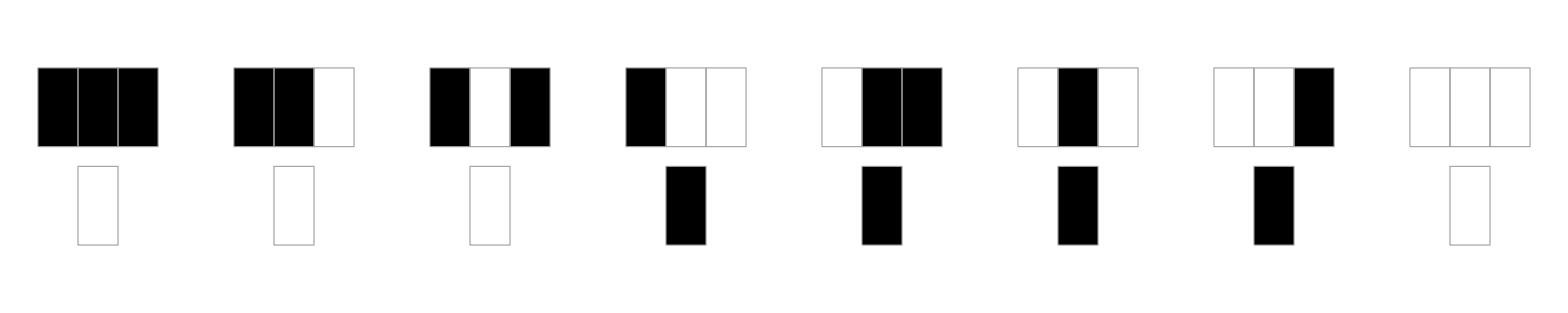

```mathematica
RulePlot[CellularAutomaton[30]]
```

However, when searching for literature that explains universality of logic gates, detailed explanation of whether they are universal or not has not been accessible to non - computing science majors. Therefore, we wrote this article to serve two purposes :
  1. Enumerate all 16 possible 2 - input, 1 - output logic gates, illustrate exhaustively each of the 16 possible gates is universal or not.
  2. Demonstrate that "computational universality", or complexity of system, is realized through the compositionality of Logical Gates. In other words, a component being classified as as a type of universal gate, would not be sufficient to support computation universally. The complexity of supporting many and all different kinds of computation comes for the composition of many of these same type of universal components. 
  
  In other words, we want to emphasize that having access to Universal Components is only a necessary but not sufficient condition to implement a Turing Complete machine. The true power of Universal Components comes from not the component itself, but its ability to be generatively composed into other kinds of computable functions. Therefore, identifying an efficient mechanism to generate and examine the equivalence of logically composable functions, is the true benefit of recognizing the "Universal Property" of Universal Logic Components. By focusing on the generative mechanism of logical functions, we can further extend this functional compositional techniques to analyze and synthesize other kinds of effective computing/simulation systems in the real world.
  
  In [Spivak 2013]: “The Operad of Wiring Diagrams”, he explicitly spelled out an NAND gate is a cospan, as depicted in this following diagram Example 2.2.11 of the corresponding paper. (The following screen capture to be removed for later editing.)
  -Graphics-

## All Possible Gates (2-input, 1-output)

Given that there are two binary valued inputs, the total number of input combinations would be 4, 2^2 is 4. For each of the 4 input combination, there would be 2 possible binary values, 1 and 0. Therefore, the total number of possible functions are 2^4=16 possible values. They can be illustrated in the following tabulated diagram:

```mathematica
functionArray=Table[{i, PadLeft[IntegerDigits[i,2],4]},{i,0,15}];
tabulatedArray=ArrayReshape[Flatten[functionArray],{16,5}];
tabulatedArray=Insert[tabulatedArray,{Item[b,Background->Red,Frame->True],1,0,1,0},1];
tabulatedArray=Insert[tabulatedArray,{Item[a,Background->Red,Frame->True],1,1,0,0},1]//Transpose;
Grid[tabulatedArray, Frame -> All,Background->{None,{Yellow}}]
```

a | b | 0 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15
1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1
0 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 1
0 | 0 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1

An alternative way of showing all these functions can be done iteratively using Mathematica’s built-in BooleanFunction and BooleanConvert.

```mathematica
Grid[Table[{c,BooleanConvert[BooleanFunction[c,2],"DNF"][a,b]//TraditionalForm}, {c,0,15,1}], Frame-> All]
```

0 | False
1 | ¬a∧¬b
2 | ¬a∧b
3 | ¬a
4 | a∧¬b
5 | ¬b
6 | (a∧¬b)∨(¬a∧b)
7 | ¬a∨¬b
8 | a∧b
9 | (a∧b)∨(¬a∧¬b)
10 | b
11 | ¬a∨b
12 | a
13 | a∨¬b
14 | a∨b
15 | True

The above table shows each and every Logic Gate Function can be labeled with a unique corresponding number. This article inherits the naming convention of Wolfram Automata, calling each Logic Gate a “rule”, then, Rule 0 and Rule 15 are the “zero” and “one” Constant Functions. Rule 1 is equivalent to NAND Gate, Rule 14 is OR gate, Rule 9 is EQUAL gate, and so on . To classify these 16 functions, we can divide them into five groups, Constants, Filter, Comparison, And-Or, Negation. These four groups can be listed in the following table:

```mathematica
groupedData={{"Group", "Constants", "Filter", "Comparison","And-OR", "Negation" }
,{"Qualifying Rules", {0, 15}, {3,5,10,12}, {6,9},{8,14}, {1,2,4,7,11,13}},
{"Names of equivalent boolean operations", {False,True},{!a, !b, b, a}//TraditionalForm,{"XOR","NXOR"},{{a &&b, a||b},{"AND", "OR"}}//TraditionalForm,{!(a||b), !a||b, !a&&b, !(a&&b), a||!b, a&&!b}//TraditionalForm}};
Grid[groupedData, Frame-> All, Background -> {None,{Yellow}}]
```

Group | Constants | Filter | Comparison | And-OR | Negation
Qualifying Rules | {0,15} | {3,5,10,12} | {6,9} | {8,14} | {1,2,4,7,11,13}
Names of equivalent boolean operations | {False,True} | {¬a,¬b,b,a} | {XOR,NXOR} | (a∧b | a∨b
AND | OR) | {¬(a∨b),¬a∨b,¬a∧b,¬(a∧b),a∨¬b,a∧¬b}

It is useful to arrange these gates/rules into separate groups. One can quickly see that gates in each group possess similar qualities. It will also be easier for us to provide proofs to each group of gates. The table listed above, the first group is the Constant group. The word Constant, means that regardless of input values, the outputs would consistently be either one or zero. Therefore, these gates cannot be universal, since they are simply static values. The four Filter gates, basically choose one input signal to the output and ignore the other. Therefore, these gates will never combine information from two separate input sources. This reduce the 2-input, 1-output gates back into a 1-input, 1-output gates, therefore, they are not universal. In other words all Filter gates are do not provide the ability to compose information. The third group compares the value presented by two input sources, and determine whether they are equal or not equal. The fourth group compose A and B inputs, however, they cannot produce the NOT operation, therefore, it cannot be composed into gates that requires the effects of NOT gate. The fifth group are the rules with two input variables and has each has at least some negation operations, they are all Universal Gates. In other words, the group of negation gates coincides with the group of universal logic gates. 
A note on negation
It is useful to note that, for using one arithmetic instruction to construct Universal Calculations, a negative sign (minus) is sufficient to create arbitrary arithemetic expressions. Therefore, negation is necessary not only in boolean values, but also in arithemtic number systems. When one relates logic with geometry, logical negation can be associated with twisted shapes like Moebius Strip. On the other hand, the ability to flip certain values provides the opportunity to create universal logic gates or universally composable shapes.

## Rules of Composition

To create different functions using one type of Universal Logic Gate, we need to define the rule of composition. One must follow these rules:
1. All derived logic gates must all be made of the same 2-input,1-output gate type.

2. The same input signal can be duplicated (copied) to both inputs of the same gate, or copied to different gates. This signal duplication operation can also be considered as an “co-relation? co-span? co-unit?” operation. See John Baez and Brendan Fong’s <A Compositional Framework For Passive Networks>.

This duplicating signal phenomenon can be thought of as both input sources having synchronized values, the resulting truth value table can be seen here:

```mathematica
oneInputArray = Drop[tabulatedArray, {3,4}];
Grid[oneInputArray, Frame -> All,Background->{None,{Yellow}}]
```

a | b | 0 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15
1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
0 | 0 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1

From the tabulated results, one may observe that out of 16 possible gates, 8 of them have constant outputs (only TRUE or FALSE). This means that, by synchronizing input sources, one can create certain constant values. For rule 1(NOR), 3(!a), 5(!b), and 7(NAND), these four gates produce negated values compared to the inputs, therefore, these four gates can be thought of being able to resemble NOT gates.

3. Different signals (a and b) cannot be directly connected to the same input port.

It is rather trivial to implement an exhaustive algorithm that associates one rule number to each 2-input, 1-output logic gates for all 16 gates. We define a function: generic2to1LogicGate[boolean, boolean, Integer(1-16)], this function is similar to the Mathematica built-in BooleanFunction.

```mathematica
intArray = Table[PadLeft[IntegerDigits[i,2],4],{i,0,15}];
boolArray = Map[If[#==0, False, True]&, intArray,{2}];
inputConfigIdx=4-(If[#1,2,0]+ If[#2,1,0])&;
generic2to1LogicGate= Function[{a,b, n},boolArray⟦n⟧⟦inputConfigIdx[a,b]⟧];
Manipulate[Grid[{{},{BooleanConvert[BooleanFunction[c-1,2][a,b],"DNF"]//TraditionalForm  , "=",generic2to1LogicGate[x, y, c]}}], {{x,False,"a"}, {False,True}},{{y,False,"b"},{False, True}},{c,1,16,1}]
```

By following the rule of composition, we can derive the relationship of all sixteen gates.

It is known that constants cannot reflect the unknown input information, therefore, rule 0 and 15 must be terminal nodes. {0,15}

It is also known that rule 3,5 are negation rules for one input source only, and they are equivalent. They also can be used to emulate a NOT gate. Similarly, rule 10 and 12 are two equivalent rules. They can be used to replace each other. 

For rule 6 and 9, they are the not-equal and equal operation. So that when providing the same signal to both inputs, it will output False and True respectively. In other words, rule 6 and 9 are connected to 0 and 15 separately.  Moreover, 6 can produce a composite gate, so that it would be able to emulate a single input gate, 10 and 12. Conversely, 9 can produce a composite gate that also emulates 10 and 12.

For rule 8 and 14, when supplied with the same signal, it will produce 10, 12. 

The remaining rules, 1,2,4,7,11,13 will be able to emulate all 16 gates.

Therefore the adjacency information can be shown as follows:

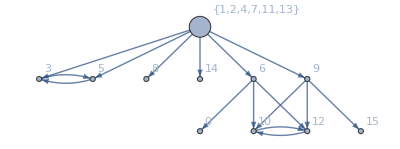

```mathematica
booleanFunctionLabel[i_]:= BooleanConvert[BooleanFunction[i,2],"DNF"][a,b]//TraditionalForm
gateDependency= { 3 -> 5, 5->3, 10->12, 12->10, 6 -> 0, 9-> 15, 6->10, 6-> 12, 9->10, 9->12, "Universal"->3, "Universal"-> 5,"Universal"->8, "Universal"-> 14,1"Universal"-> 6, "Universal"->9};
LayeredGraphPlot[gateDependency, VertexLabels->{"Name", "Universal" -> "{1,2,4,7,11,13}"}, VertexSize-> {"Universal" -> Large}]
```

The same dependency graph can be drawn with associated boolean expressions.

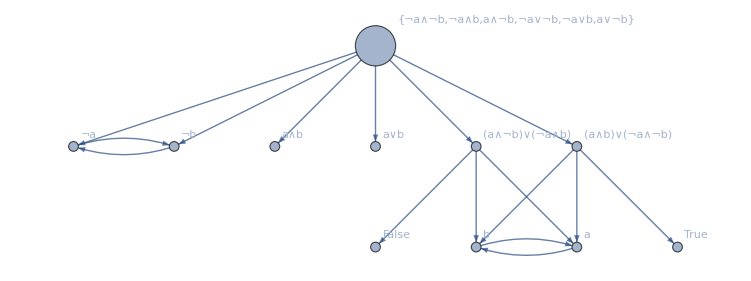

```mathematica
graphWithExpression =gateDependency /. Table[i-> booleanFunctionLabel[i],{i,0,15}];
LayeredGraphPlot[graphWithExpression, VertexLabels->{"Name", "Universal" ->  "{¬a∧¬b,¬a∧b,a∧¬b,¬a∨¬b,¬a∨b,a∨¬b}"}, VertexSize-> {"Universal" -> Large}]
```

## Categorical Logic Gates (A Lattice of Boolean Functions)

Based on the dependency diagram shown above, the dependency structure is indeed a reachability diagram of functional composition. For example, the True and False nodes cannot be composed into any other logic gates, therefore these two nodes will not be able to reach other nodes from their positions. Clearly, the 6 universal logic gates can reach down to any of the other 10 nodes.

This reachability diagram can also be used as a foundation to categorize logic gates. It also provides a mean to categorize the properties of different kinds of logic gates. Visually, the diagram appears to have a total of 8 distinct groups of nodes, in fact, it is only 5. Since it differs from the 5 groups, due to the fact that True and False are categorized as two distinct groups. And (a,b), (!a, !b) are considered to be two separate groups.

Universality through topological relations
One way of using the adjacency diagram of the 16 logic gate, is to think of them as topological relationships. If two nodes are connected with each other, then, they can emulate each other’s function. For example, (!a) can emulate (!b), and XOR can emulate (a) and (b). These connections also shows that  one input and one output Logic Gates, there are only two types of possible functions. The identity function, where input values must equal to output values. The other one is the inversion function, that inverts the value of true to false and false to true. Therefore all the possible outcomes for one input source is rather trivial. We call these gates, the trivial Gate type. They are constants or negation of a given value.
The second class of logic gates have two input sources and one output. This type gates have a total of 16 possible variations. The number 16 comes from the following exponents of a Hom-Set, B(input, output). There is only one set of input combinations, (A,B). There are 2^4 possible different functions given these four different input values. 

Out of the 16 gates, or 2 input one output functions, there are only three types of gates. Constant, Trivial, and Universal Gates. We list them as follows:

In the Constant  results, where all possible input combinations turns into one or zero. These Constants account for two gates in the total 16 possible variations.

The  Trivial Type, AND gate, OR gate, Equal gate (XNOR), Not Equal (XOR) gate, and the two gates that only reflect the values of As and Bs. 

Finally, the  Universal Gates. There are total of 6 different ones. NAND, NOR, and four other variants, that can be represented as one group: {a && !b, a || ~b, !a&&b, !a || b}.

```mathematica
Outline of the proof
```

We know that universal logic gates are gates that can be composed into any of the 16 gates. To show that NAND gates and other Universal Logic Gates are universal, we can simply show that Universal types of gates can be converted into NAND or NOR gates. Then, we can just argue that since NAND or NOR are universal, the other gates that can be converted to NAND or NOR must also be Universal. It requires no efforts in explaining that Constant types are immutable, they are just static values. We only need to show that trivial types can only be composed into Constant values, or they can only be composed into Trivial Gates. Within the trivial gate types there are total of 6 different gates. Let us perform proof on each one of them.

```mathematica
Testing Universality
```

All sixteen gates have two boolean inputs, A and B. Each gate can only produce one boolean value C, but this output value can be connected to many possible inputs, since we allow the same component type to participate in the computational task. The total number of components is not limited, but to conserve the space of design effort, when we see a repeatable pattern, we will stop expanding the number of participating component. To save the effort of proof, we also allow static values to be used as input. Since static values can be assigned as initial values, and they will not change over time by definition. For the first two groups, we know they can only produce trivial results that cannot be Universal Components. Therefore, we will focus on the proofs of the last three groups of gates.

```mathematica
XOR gate
```

The gate, XOR, can be thought of as the NOT EQUAL operator in logic. In other words, when A and B holds different values, it returns true, and when A and B have equal values, then XOR returns false. Meaning that it is a comparison operator that reflects that two values cannot be equal. takes two boolean variables, A and B, and produce one boolean value C. This gate cannot

```mathematica
AND gate is trivial
```

The gate, AND, takes two boolean variables, A and B, and produce one boolean value C. This gate cannot

```mathematica
AND gate is trivial
```

The gate, AND, takes two boolean variables, A and B, and produce one boolean value C. This gate cannot

```mathematica
AND gate is trivial
```

The gate, AND, takes two boolean variables, A and B, and produce one boolean value C. This gate cannot

This paper will draw on a few mathematical fields, including boolean logic, topology, and  engineering practice, and quantum mechanics, as a finite set of content that are deeply related to the compositionality of Universal Logic Gates. A of digital circuits, framework of coProperties of 

 It is even less well known that, the universality property of a simple building component, such as NAND, can be used as the basic measuring stick for complexity of electric circuit, and for 

 There are three types of Logic Gates : constants, simple/trivial gates, and Universal Gates. Given a two input one output Logic Gate, there are total of 16 gates. We can For constants, there are only two possible values, true/false. For Trivial Gates, there are total of

## Composable Logic Gates

We describe Logic Gates as composable functions, if it can take logical values as inputs and create logical values as outputs. Based Category Theory, logical functions are composable, if they are Monoids. Meaning that all the domains and co-domains are in the domain of boolean values, only (truth/false) two possible binary values. The interesting idea here is that designing logic gates can be turned into a simple enumeration procedure. So that machines, not human cognitive processes, can automatically identify all the possible Universal Component/Gates can be created. As it turns out, all Logical Gates can be constructed based on two inputs and one output gates. This simple assertion is important, Logic Gates must be able to at least combine two inputs to perform a “composition” of values. And out of two input one output gates, there are total of only 16 gates. Of the 16 gates, there are only three types. It is important to classify the gates in terms of types. It provides a way to offer a different level of reasoning about functions, while also showing that functions can be computed. Functions or logic gates are objective mathematical entities that can be enumerated, composed and categorized using mechanical rules, not just created written by mythical human opinions. 
The Simple Logic Gates
For one input and one output Logic Gates, there are only two types of possible functions. The identity function, where input values must equal to output values. The other one is the inversion function, that inverts the value of true to false and false to true. Therefore all the possible outcomes for one input source is rather trivial. We call these gates, the trivial Gate type. They are constants or negation of a given value.
The second class of logic gates have two input sources and one output. This type gates have a total of 16 possible variations. The number 16 comes from the following exponents of a Hom-Set, B(input, output). There is only one set of input combinations, (A,B). There are 2^4 possible different functions given these four different input values. 

Out of the 16 gates, or 2 input one output functions, there are only three types of gates. Constant, Trivial, and Universal Gates. We list them as follows:

In the Constant  results, where all possible input combinations turns into one or zero. These Constants account for two gates in the total 16 possible variations.

The  Trivial Type, AND gate, OR gate, Equal gate (XNOR), Not Equal (XOR) gate, and the two gates that only reflect the values of As and Bs. 

Finally, the  Universal Gates. There are total of 6 different ones. NAND, NOR, and four other variants, that can be represented as one group: {A& ~B, A | ~B, ~A& B, ~A | B}.

```mathematica
Outline of the proof
```

We know that universal logic gates are gates that can be composed into any of the 16 gates. To show that NAND gates and other Universal Logic Gates are universal, we can simply show that Universal types of gates can be converted into NAND or NOR gates. Then, we can just argue that since NAND or NOR are universal, the other gates that can be converted to NAND or NOR must also be Universal. It requires no efforts in explaining that Constant types are immutable, they are just static values. We only need to show that trivial types can only be composed into Constant values, or they can only be composed into Trivial Gates. Within the trivial gate types there are total of 6 different gates. Let us perform proof on each one of them.

```mathematica
Compositional Rules
```

All sixteen gates have two boolean inputs, A and B. Each gate can only produce one boolean value C, but this output value can be connected to many possible inputs, since we allow the same component type to participate in the computational task. The total number of components is not limited, but to conserve the space of design effort, when we see a repeatable pattern, we will stop expanding the number of participating component. To save the effort of proof, we also allow static values to be used as input. Since static values can be assigned as initial values, and they will not change over time by definition.

```mathematica
XOR gate
```

The gate, XOR, can be thought of as the NOT EQUAL operator in logic. In other words, when A and B holds different values, it returns true, and when A and B have equal values, then XOR returns false. Meaning that it is a comparison operator that reflects that two values cannot be equal. takes two boolean variables, A and B, and produce one boolean value C. This gate cannot

```mathematica
AND gate is trivial
```